# Лабораторная работа №2

## Воинов Владислав, 421701 Вариант 9

## Задание 1. Создать таблицу значений функции f(x), разбив отрезок [1,3] на n равных частей точками x_i (i=0,...,n). Для полученной таблично заданной в равноотстоящих узлах функции f(x) выполнить следующие действия при n=6 и n=10.

```mathematica
(* ===Задание 1:Блок 0. Инициализация и утилиты===*)(*1) Чистим только нужные символы (без трогания системных Pi/Sin/Plot)*)ClearAll[a,b,img,f,eqGrid,eqData,eqPoly,pts];

(*2) Базовые определения варианта 9*)
a=1;                             (*левая граница[1,3]*)
b=3;                            (*правая граница*)
img=800;                         (*размер картинок*)

(*f(x)=Log[x]—определяем как обычную числовую функцию*)
f[x_?NumericQ]:=Log[x];

(*3) Равноотстоящие узлы:сразу численно,чтобы не тянуть символику*)
eqGrid[n_Integer?NonNegative]:=N@Table[a+i (b-a)/n,{i,0,n}];

(*4) Табличные данные (x_i,f(x_i))—численно*)
eqData[n_Integer?NonNegative]:=With[{xs=eqGrid[n]},Transpose[{xs,N@(f/@xs)}]];

(*5) Интерполяционный полином по данным (без Simplify)*)
eqPoly[n_Integer?NonNegative]:=InterpolatingPolynomial[eqData[n],x];

(*6) Утилита для отрисовки узлов*)
pts[data_List]:=ListPlot[data,PlotStyle->Black,PlotMarkers->Automatic];

(*7) ДЫМО-ТЕСТ:проверим,что всё определилось корректно*)
Print["[SMOKE] grid(6) len = ",Length@eqGrid[6],", first pair = ",First@eqData[6]];
Print["[SMOKE] eqPoly(6) eval at 1.0 -> ",N@(eqPoly[6]/. x->1.0)];
```

[SMOKE] grid(6) len = 7, first pair = {1.,0.}

[SMOKE] eqPoly(6) eval at 1.0 -> 0.

### а) Построить интерполяционный многочлен Лагранжа (L_n(x)), проиллюстрировать графически (при (n=6)).

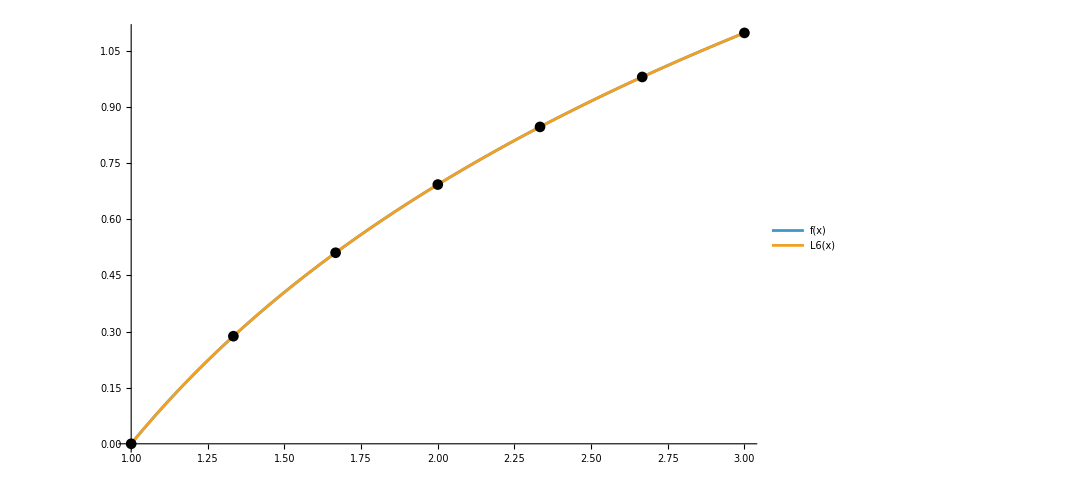

```mathematica
n=6;
data6=eqData[n];
Ln6[x_]=eqPoly[n]//Simplify;
Show[Plot[{f[x],Ln6[x]},{x,a,b},PlotLegends->{"f(x)","L6(x)"},ImageSize->img],pts[data6]]
```

### б) Создать таблицу разделённых разностей функции (f(x)) по точкам ((x_i,f(x_i))) (при (n=6)).

```mathematica
TableForm[data6,TableHeadings->{Range[0,n],{"x_i","f(x_i)"}}]
```

| x_i | f(x_i)
0 | 1. | 0.
1 | 1.33333 | 0.287682
2 | 1.66667 | 0.510826
3 | 2. | 0.693147
4 | 2.33333 | 0.847298
5 | 2.66667 | 0.980829
6 | 3. | 1.09861

### в) Построить первый (или второй) интерполяционный многочлен Ньютона (P_n(x)), проиллюстрировать графически (при (n=6)).

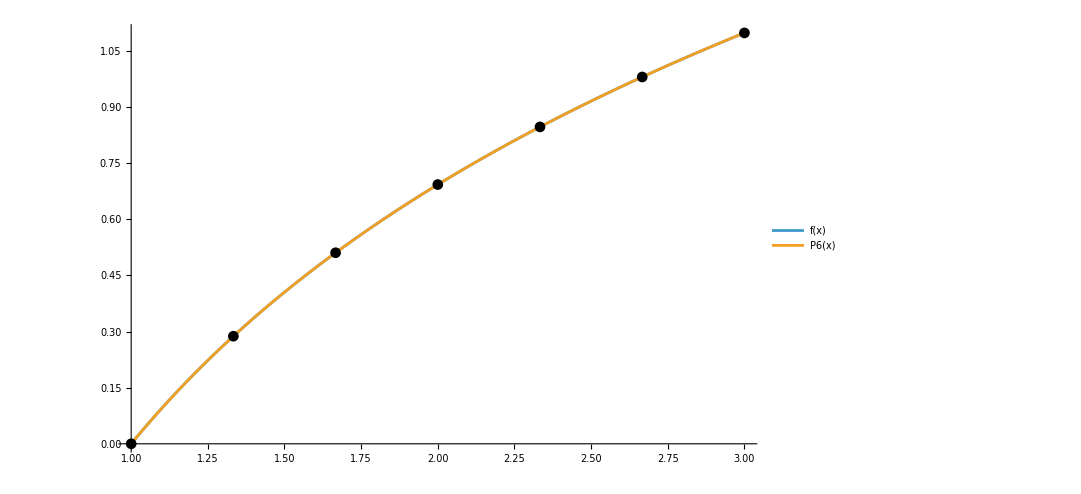

```mathematica
Pn6[x_]=eqPoly[6]//Simplify;
Show[Plot[{f[x],Pn6[x]},{x,a,b},PlotLegends->{"f(x)","P6(x)"},ImageSize->img],pts[data6]]
```

### г) Построить интерполяционный многочлен Ньютона (Npn(x)) с помощью InterpolatingPolynomial, проиллюстрировать графически (при (n=6)).

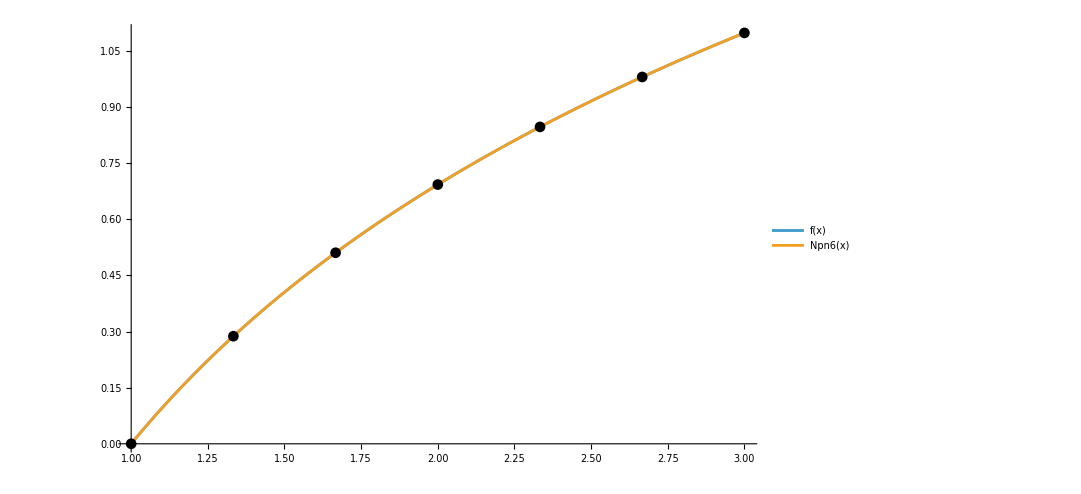

```mathematica
Np6[x_]=InterpolatingPolynomial[data6,x]//Simplify;
Show[Plot[{f[x],Np6[x]},{x,a,b},PlotLegends->{"f(x)","Npn6(x)"},ImageSize->img],pts[data6]]
```

### д) Вычислить значения (f(x)) и всех построенных многочленов в точке (x=2.4316) (при (n=6)).

```mathematica
{f[x0],Ln6[x0],Pn6[x0],Np6[x0]}//N
```

{f[x0],-1.87802+3.3447 x0-2.27574 x0^2+1.07666 x0^3-0.315592 x0^4+0.0515858 x0^5-0.00359135 x0^6,-1.87802+3.3447 x0-2.27574 x0^2+1.07666 x0^3-0.315592 x0^4+0.0515858 x0^5-0.00359135 x0^6,-1.87802+3.3447 x0-2.27574 x0^2+1.07666 x0^3-0.315592 x0^4+0.0515858 x0^5-0.00359135 x0^6}

### е) Построить график абсолютной погрешности (R_n(x)=|f(x)-Npn(x)|) на ([1,3]), найти её максимум (при (n=6)).

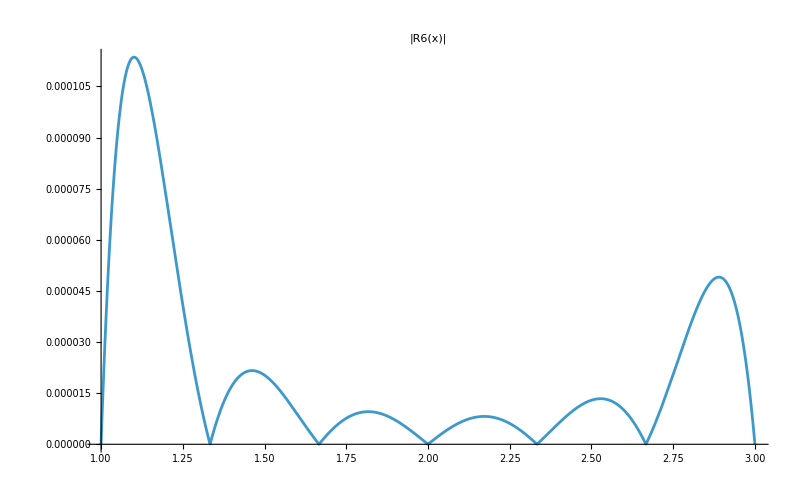

maxErr[Abs[1.87802-3.3447 x+2.27574 x^2-1.07666 x^3+0.315592 x^4-0.0515858 x^5+0.00359135 x^6+f[x]]]

```mathematica
Rn6[x_]=Abs[f[x]-Np6[x]];
Plot[Rn6[x],{x,a,b},PlotLabel->"|R6(x)|",ImageSize->img]
maxRn6=maxErr[Rn6[x]]  (*{максимум,{x->точка}}*)
```

### ж) Повторить пункты а–е для (n=10).

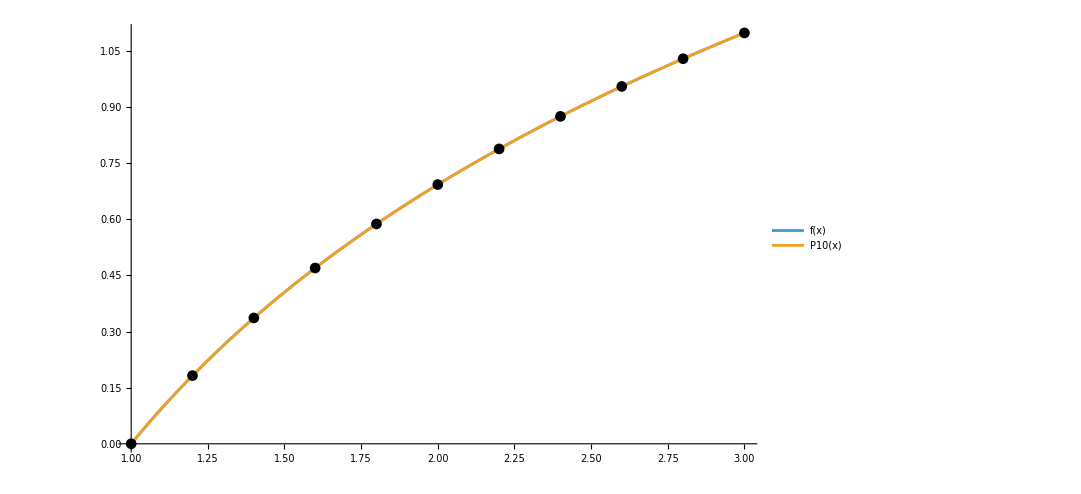

{f[x0],-2.34611+5.54648 x0-6.83329 x0^2+6.56926 x0^3-4.60645 x0^4+2.33501 x0^5-0.846508 x0^6+0.214069 x0^7-0.0358796 x0^8+0.00358281 x0^9-0.000161372 x0^10,-2.34611+5.54648 x0-6.83329 x0^2+6.56926 x0^3-4.60645 x0^4+2.33501 x0^5-0.846508 x0^6+0.214069 x0^7-0.0358796 x0^8+0.00358281 x0^9-0.000161372 x0^10,-2.34611+5.54648 x0-6.83329 x0^2+6.56926 x0^3-4.60645 x0^4+2.33501 x0^5-0.846508 x0^6+0.214069 x0^7-0.0358796 x0^8+0.00358281 x0^9-0.000161372 x0^10}

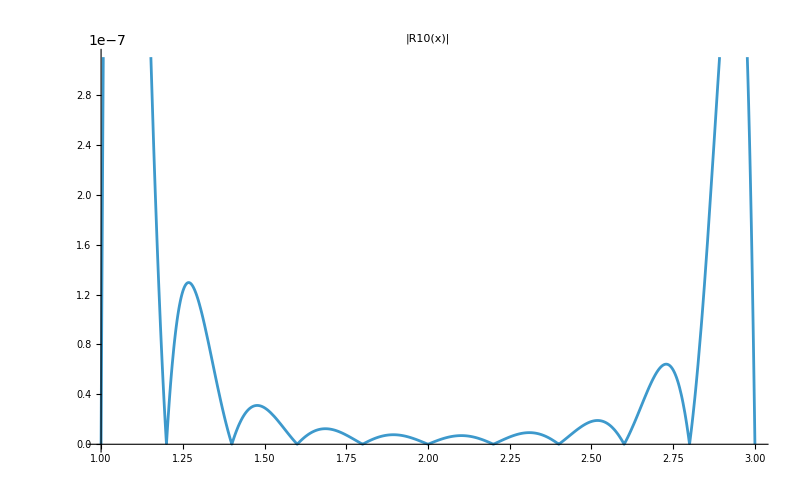

maxErr[Abs[2.34611-5.54648 x+6.83329 x^2-6.56926 x^3+4.60645 x^4-2.33501 x^5+0.846508 x^6-0.214069 x^7+0.0358796 x^8-0.00358281 x^9+0.000161372 x^10+f[x]]]

```mathematica
n=10;
data10=eqData[n];

Ln10[x_]=eqPoly[n]//Simplify;
Pn10[x_]=Ln10[x];
Np10[x_]=InterpolatingPolynomial[data10,x]//Simplify;

Show[Plot[{f[x],Pn10[x]},{x,a,b},PlotLegends->{"f(x)","P10(x)"},ImageSize->img],pts[data10]]

{f[x0],Ln10[x0],Pn10[x0],Np10[x0]}//N

Rn10[x_]=Abs[f[x]-Np10[x]];
Plot[Rn10[x],{x,a,b},PlotLabel->"|R10(x)|",ImageSize->img]
maxRn10=maxErr[Rn10[x]]
```

## Задание 2. Создать таблицу значений функции (f(x)), разбив отрезок ([1,3]) на (n) частей неравноотстоящими точками (x_i=\frac{a+b}{2}+\frac{b-a}{2}t_i), где (t_i) — корни многочлена Чебышёва (T_{n+1}(t)). Для полученной функции выполнить действия при (n=6) и (n=10).

```mathematica
chebGrid[n_]:=Table[(a+b)/2+(b-a)/2*Cos[(2 k+1) Pi/(2 (n+1))],{k,0,n}];
chebData[n_]:=With[{xs=chebGrid[n]},Transpose[{xs,f/@xs}]];
chebPoly[n_]:=InterpolatingPolynomial[chebData[n],x];
```

#### а) Создать таблицу разделённых разностей по чебышёвским узлам (при (n=6)).

```mathematica
ndata6=chebData[6];
TableForm[ndata6,TableHeadings->{None,{"x_k (Cheb)","f(x_k)"}}]
```

x_k (Cheb) | f(x_k)
2+Cos[π/14] | Log[2+Cos[π/14]]
2+Cos[(3 π)/14] | Log[2+Cos[(3 π)/14]]
2+Sin[π/7] | Log[2+Sin[π/7]]
2 | Log[2]
2-Sin[π/7] | Log[2-Sin[π/7]]
2-Cos[(3 π)/14] | Log[2-Cos[(3 π)/14]]
2-Cos[π/14] | Log[2-Cos[π/14]]

#### б) Построить интерполяционный многочлен Ньютона (P^{(r)}_n(x)) (при (n=6)), проиллюстрировать графически.

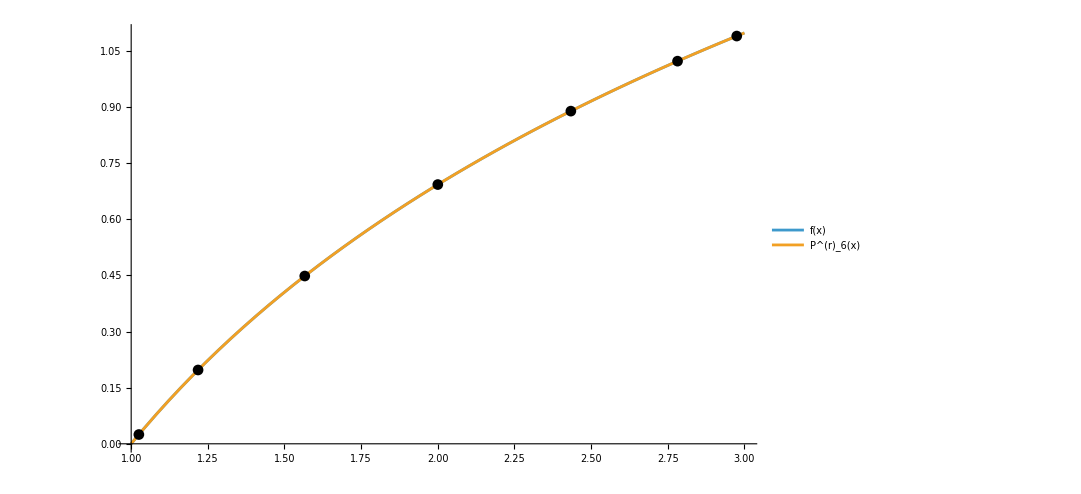

```mathematica
(* ===Задание 2,б)—P^(r)_n(x),n=6,Чебышёвские узлы+график===*)Module[{a,b,f,n,chebGrid,xs,ys,ndata6,Prn6,img=800},a=1;b=3;
f[x_]:=Log[x];
n=6;
(*Узлы Чебышёва и значения—строго численно*)chebGrid[m_Integer]:=N@Table[(a+b)/2+(b-a)/2*Cos[(2 k+1) Pi/(2 (m+1))],{k,0,m}];
xs=chebGrid[n];
ys=N@(f/@xs);
ndata6=Transpose[{xs,ys}];
(*Интерполяционный полином по неравномерным узлам (без Simplify)*)
Clear[Prn6];
Prn6[x_]=InterpolatingPolynomial[ndata6,x];
(*График f и P^(r)_6+точки узлов*)Show[Plot[{f[x],Prn6[x]},{x,a,b},PlotLegends->{"f(x)","P^(r)_6(x)"},ImageSize->img],ListPlot[ndata6,PlotStyle->Black,PlotMarkers->Automatic]]]
```

#### в) Построить интерполирующую функцию Intf_n(x) с помощью Interpolation (при (n=6)), проиллюстрировать графически.

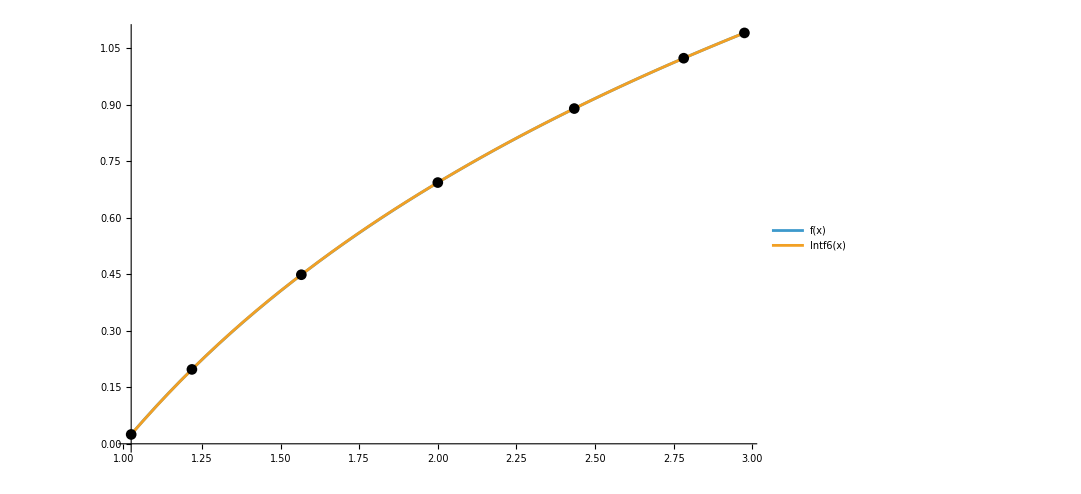

```mathematica
(* ===Задание 2,в):Intf6(x) по чебышёвским узлам,график без экстраполяции===*)Module[{a,b,f,n,img=800,xs,ys,ndata6,Intf6,min6,max6},(*Функция и интервал варианта 2*)a=1;b=3;
f[x_]:=Log[x];
n=6;
(*Чебышёвские узлы на[a,b]—сразу в численном виде*)xs=N@Table[(a+b)/2+(b-a)/2*Cos[(2 k+1) Pi/(2 (n+1))],{k,0,n}];
(*Табличные значения функции в узлах (численно)*)ys=N@(f/@xs);
ndata6=Transpose[{xs,ys}];
(*Интерполирующая функция по неравномерным узлам*)Intf6=Interpolation[ndata6];
(*Реальный домен интерполирующей функции (узлы не включают концы[a,b])*)min6=Min[xs];
max6=Max[xs];
(*График f(x) и Intf6(x) БЕЗ экстраполяции+точки-узлы*)Show[Plot[{f[x],Intf6[x]},{x,min6,max6},PlotLegends->{"f(x)","Intf6(x)"},ImageSize->img],ListPlot[ndata6,PlotStyle->Black,PlotMarkers->Automatic]]]
```

#### г) Вычислить значения (f(x)), (P^{(r)}_n(x)), Intf_n(x) в точке (x=2.4316) (при (n=6)); найти максимумы (|f-P^{(r)}_n|) и (|f-\text{Intf}_n|) на ([1,3]).

```mathematica
{f[x0],Prn6[x0],Intf6[x0]}//N
R6cheb[x_]=Abs[f[x]-Prn6[x]];
R6int[x_]=Abs[f[x]-Intf6[x]];
{maxErr[R6cheb[x]],maxErr[R6int[x]]}
```

{f[x0],Prn6[x0],Intf6[x0]}

{maxErr[Abs[f[x]-Prn6[x]]],maxErr[Abs[f[x]-Intf6[x]]]}

#### д) Повторить пункты а)–г) для (n=10).

x_k (Cheb) | f(x_k)
2.98982 | 1.09521
2.90963 | 1.06803
2.75575 | 1.01369
2.54064 | 0.932416
2.28173 | 0.824935
2. | 0.693147
1.71827 | 0.541316
1.45936 | 0.377997
1.24425 | 0.218533
1.09037 | 0.0865153
1.01018 | 0.0101271

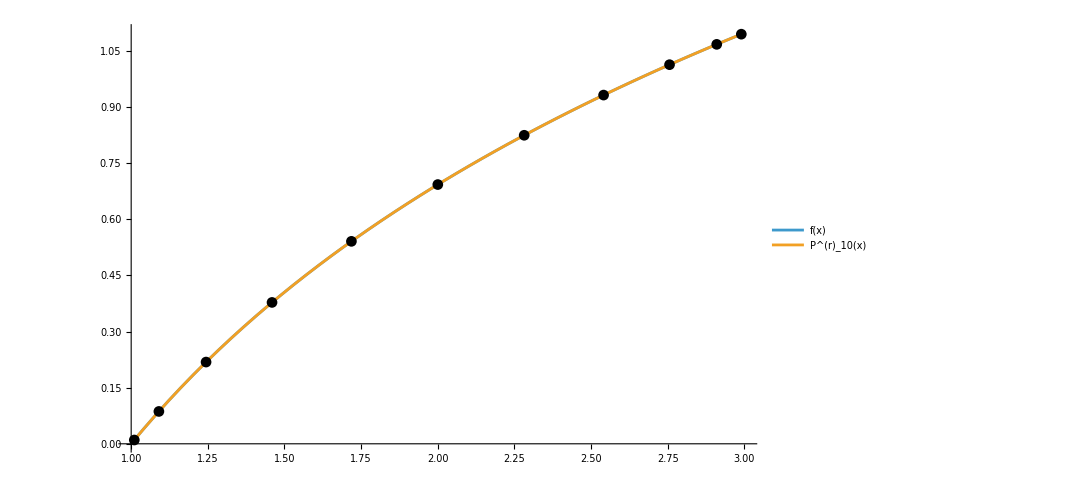
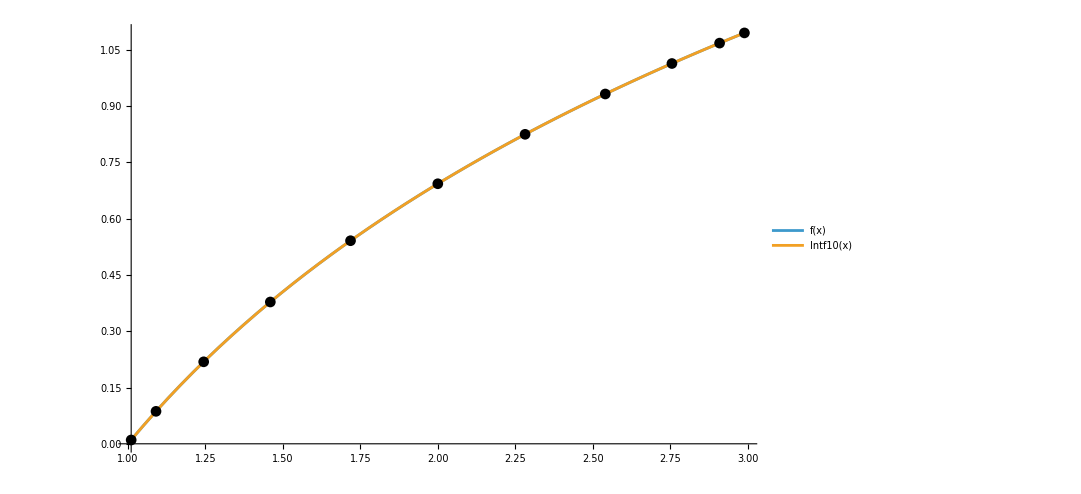

```mathematica
(* ===Задание 2,д):повтор а)–в) для n=10—таблица,P^(r)_10,Intf10===*)Module[{a,b,f,n,chebGrid,xs,ys,ndata10,Prn10,Intf10,img=800,min10,max10,g1,g2},a=1;b=3;
f[x_]:=Log[x];
n=10;
(*а) Таблица узлов Чебышёва и значений—строго численно*)chebGrid[m_Integer]:=N@Table[(a+b)/2+(b-a)/2*Cos[(2 k+1) Pi/(2 (m+1))],{k,0,m}];
xs=chebGrid[n];
ys=N@(f/@xs);
ndata10=Transpose[{xs,ys}];
Print@TableForm[ndata10,TableHeadings->{None,{"x_k (Cheb)","f(x_k)"}}];
(*б) Интерполяционный многочлен Ньютона P^(r)_10*)Prn10[x_]=InterpolatingPolynomial[ndata10,x];(*без Simplify*)g1=Show[Plot[{f[x],Prn10[x]},{x,a,b},PlotLegends->{"f(x)","P^(r)_10(x)"},ImageSize->img],ListPlot[ndata10,PlotStyle->Black,PlotMarkers->Automatic]];
(*в) Интерполирующая функция Intf10 на реальном домене*)Intf10=Interpolation[ndata10];
min10=Min[xs];
max10=Max[xs];
g2=Show[Plot[{f[x],Intf10[x]},{x,min10,max10},PlotLegends->{"f(x)","Intf10(x)"},ImageSize->img],ListPlot[ndata10,PlotStyle->Black,PlotMarkers->Automatic]];
(*Возвращаем оба графика для вывода*){g1,g2}]
```

## Задание 3. Выполнить интерполяцию функции (f(x)) сплайном (S_f(x)) с помощью Interpolation[data, Method -> “Spline”], используя таблицу значений в равноотстоящих точках для (n=5) и (n=10).

### а) Построить графики (f(x)), узлов и (S_f(x)) (при (n=5)); построить (|f-S_f|) и найти максимум на ([1,3]).

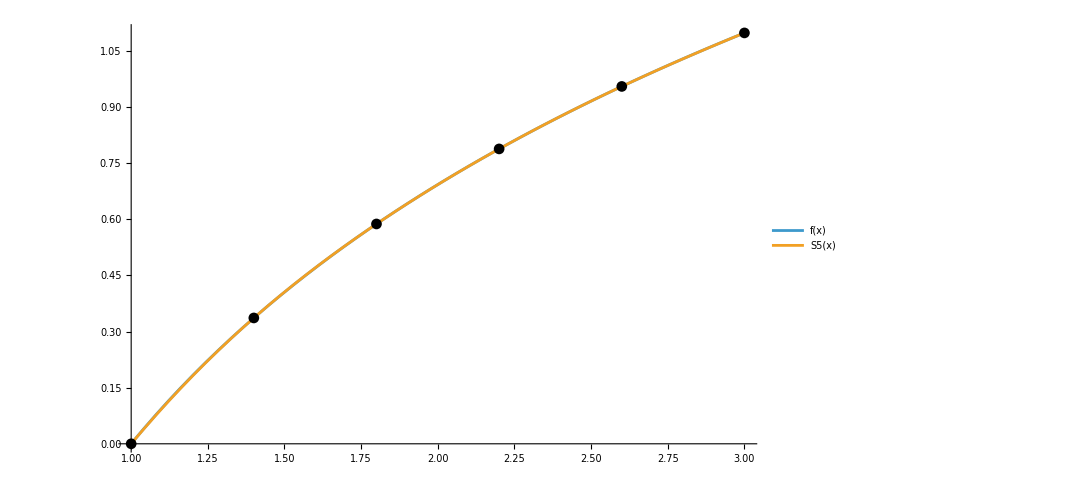

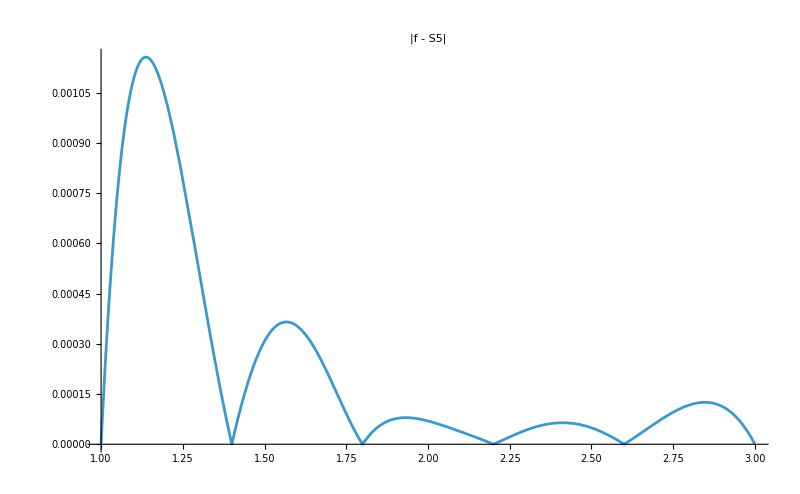

{0.0000794481,{x→1.93219}}

```mathematica
(*Равномерные узлы и сплайн для n=5*)
eqGrid[n_Integer]:=Table[a+i (b-a)/n,{i,0,n}];
eqData[n_Integer]:=With[{xs=eqGrid[n]},Transpose[{xs,N@(f/@xs)}]];

n=5;
data5=eqData[n];
Sf5=Interpolation[data5,Method->"Spline"];
img=800;

Show[Plot[{f[x],Sf5[x]},{x,a,b},PlotLegends->{"f(x)","S5(x)"},
ImageSize->img],ListPlot[data5,PlotStyle->Black,PlotMarkers->Automatic]]

R5s[x_]:=Abs[f[x]-Sf5[x]];
Plot[R5s[x],{x,a,b},PlotLabel->"|f - S5|",ImageSize->img]

(*Безопасный максимум*)
maxErr[expr_,{xl_,xr_}]:=Quiet@Check[FindMaximum[{expr,xl<=x<=xr},{x,(xl+xr)/2}],
With[{xs=Subdivide[xl,xr,800]},Module[{vals=Abs[expr/. x->xs],i},i=Ordering[vals,-1][[1]];
{vals[[i]],{x->xs[[i]]}}]]];

maxR5s=maxErr[R5s[x],{a,b}]
```

### б) Повторить пункт а) для (n=10).

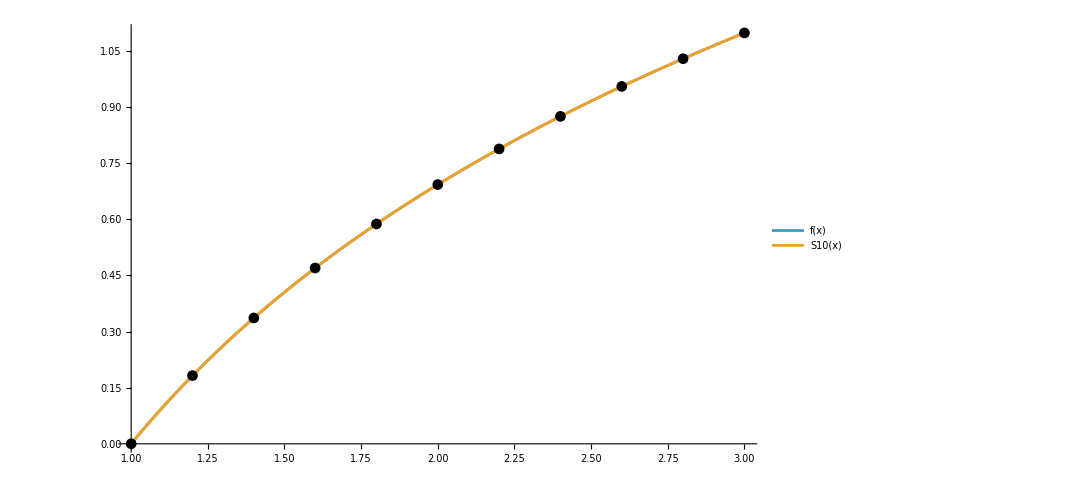

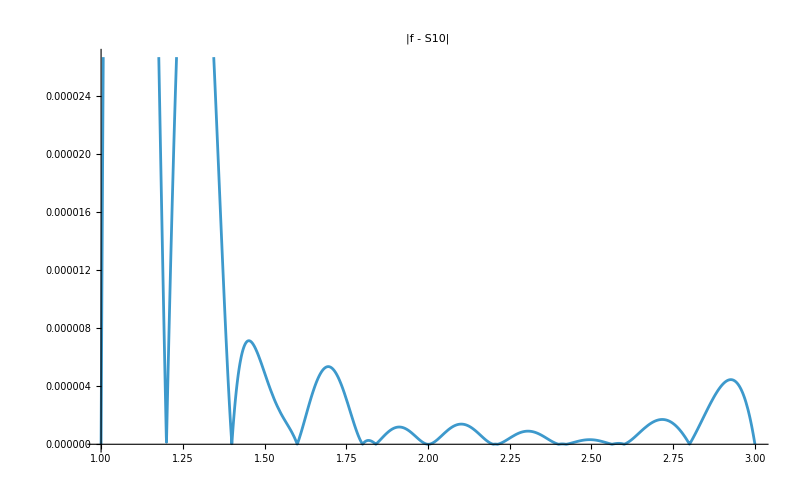

{3.65691×10^-11,{x→1.99996}}

```mathematica
(*Равномерные узлы и сплайн для n=10*)n=10;
data10=eqData[n];
Sf10=Interpolation[data10,Method->"Spline"];

Show[Plot[{f[x],Sf10[x]},{x,a,b},PlotLegends->{"f(x)","S10(x)"},
ImageSize->img],ListPlot[data10,PlotStyle->Black,PlotMarkers->Automatic]]

R10s[x_]:=Abs[f[x]-Sf10[x]];
Plot[R10s[x],{x,a,b},PlotLabel->"|f - S10|",ImageSize->img]

maxR10s=maxErr[R10s[x],{a,b}]
```

## Задание 4. Составить таблицу максимальных значений погрешности (R_n(x)) для разных (n) по результатам заданий 1–3. Сравнить для равноотстоящих и неравноотстоящих узлов и сплайна.

```mathematica
(* ===Задание 4:таблица Max|ошибки|для Equal/Chebyshev/Spline===*)Module[{a=1,b=3,img=800,f,eqGrid,eqData,eqPolyNum,chebGrid,chebData,chebPolyNum,splineInterpNum,maxErr,eqNs,chebNs,splineNs,eqMaxTbl,chebMaxTbl,splineMaxTbl,maxErrTable},(*Функция варианта 2*)f[x_]:=Log[x];
(*Равноотстоящие узлы и интерполянт (численно)*)eqGrid[n_Integer]:=N@Table[a+i (b-a)/n,{i,0,n}];
eqData[n_Integer]:=With[{xs=eqGrid[n]},Transpose[{xs,N@(f/@xs)}]];
eqPolyNum[n_Integer]:=InterpolatingPolynomial[eqData[n],x];(*без Simplify*)(*Узлы Чебышёва и интерполянт (численно)*)chebGrid[n_Integer]:=N@Table[(a+b)/2+(b-a)/2*Cos[(2 k+1) Pi/(2 (n+1))],{k,0,n}];
chebData[n_Integer]:=With[{xs=chebGrid[n]},Transpose[{xs,N@(f/@xs)}]];
chebPolyNum[n_Integer]:=InterpolatingPolynomial[chebData[n],x];(*без Simplify*)(*Сплайн по равноотстоящим узлам*)splineInterpNum[n_Integer]:=Interpolation[eqData[n],Method->"Spline"];
(*Надёжный максимум с fallback на сетку*)maxErr[expr_,{xl_,xr_}]:=Quiet@Check[FindMaximum[{expr,xl<=x<=xr},{x,(xl+xr)/2}],With[{xs=Subdivide[xl,xr,800]},Module[{vals=Abs[expr/. x->xs],i=Ordering[vals,-1][[1]]},{vals[[i]],{x->xs[[i]]}}]]];
(*Наборы n (как в отчётах)*)eqNs={6,10};
chebNs={6,10};
splineNs={5,10};
(*Таблицы максимумов—всё численно,без тяжёлой символики*)eqMaxTbl=Table[With[{poly=eqPolyNum[n]},{n,"Equal",maxErr[Abs[f[x]-poly],{a,b}][[1]]}],{n,eqNs}];
chebMaxTbl=Table[With[{poly=chebPolyNum[n]},{n,"Chebyshev",maxErr[Abs[f[x]-poly],{a,b}][[1]]}],{n,chebNs}];
splineMaxTbl=Table[With[{sp=splineInterpNum[n]},{n,"Spline",maxErr[Abs[f[x]-sp[x]],{a,b}][[1]]}],{n,splineNs}];
maxErrTable=SortBy[Join[eqMaxTbl,chebMaxTbl,splineMaxTbl],First];
Grid[Prepend[maxErrTable,{"n","Method","Max |Error|"}],Frame->All,ItemStyle->Directive[14]]]
```

n | Method | Max |Error|
5 | Spline | 0.0000794481
6 | Chebyshev | 0.000028181
6 | Equal | 2.64955×10^-12
10 | Chebyshev | 5.82867×10^-14
10 | Equal | 5.66214×10^-15
10 | Spline | 3.65691×10^-11

## Задание 5. Построить по МНК аппроксимирующие алгебраические многочлены наилучшего среднеквадратичного приближения (Q_1(x), Q_2(x), Q_3(x), Q_4(x)) (использовать таблицу из задания 1 при (n=10)); вывести графики вместе с (f(x)) и узлами.

### а) Построить (Q_1(x), Q_2(x), Q_3(x), Q_4(x)) и вывести их аналитический вид.

```mathematica
(* ===Задание 5а:Q1..Q4 (МНК) на равноотстоящих узлах при n=10===*)Module[{a,b,f,n,xs,ys,dataFit,Q1,Q2,Q3,Q4},a=1;b=3;
f[x_]:=Log[x];
n=10;
(*узлы и значения строго численно*)
xs=N@Table[a+i (b-a)/n,{i,0,n}];
ys=N@(f/@xs);
dataFit=Transpose[{xs,ys}];
(*аппроксимация Fit—только численные данные,без Simplify*)
Q1[x_]:=Fit[dataFit,{1,x},x];
Q2[x_]:=Fit[dataFit,{1,x,x^2},x];
Q3[x_]:=Fit[dataFit,{1,x,x^2,x^3},x];
Q4[x_]:=Fit[dataFit,{1,x,x^2,x^3,x^4},x];
(*выводим аналитический вид (с плавающими коэффициентами)*)
{"Q1(x) ="->N@Q1[x],"Q2(x) ="->N@Q2[x],"Q3(x) ="->N@Q3[x],"Q4(x) ="->N@Q4[x]}]
```

{Q1(x) =→-0.430325+0.534135 x,Q2(x) =→-0.947631+1.10892 x-0.143696 x^2,Q3(x) =→-1.28624+1.69016 x-0.452646 x^2+0.0514916 x^3,Q4(x) =→-1.53663+2.26884 x-0.92799 x^2+0.216829 x^3-0.0206671 x^4}

### б) Вывести на одном графике (f(x)), точки ((x_i,f(x_i))) и (Q_1, Q_2, Q_3, Q_4).

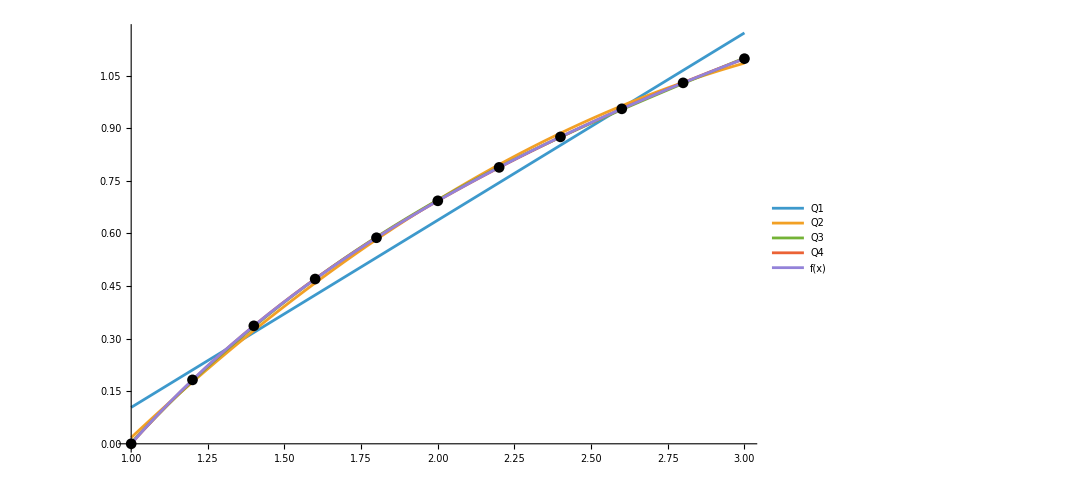

```mathematica
(* ===Задание 5б:общий график f,узлы,Q1..Q4===*)
Module[{a,b,f,n,xs,ys,dataFit,Q1,Q2,Q3,Q4,img=800},a=1;b=3;
f[x_]:=Log[x];
n=10;
xs=N@Table[a+i (b-a)/n,{i,0,n}];
ys=N@(f/@xs);
dataFit=Transpose[{xs,ys}];
Q1[x_]:=Fit[dataFit,{1,x},x];
Q2[x_]:=Fit[dataFit,{1,x,x^2},x];
Q3[x_]:=Fit[dataFit,{1,x,x^2,x^3},x];
Q4[x_]:=Fit[dataFit,{1,x,x^2,x^3,x^4},x];
Show[Plot[Evaluate[{Q1[x],Q2[x],Q3[x],Q4[x],f[x]}],{x,a,b},
PlotLegends->{"Q1","Q2","Q3","Q4","f(x)"},ImageSize->img],ListPlot[dataFit,PlotStyle->Black,PlotMarkers->Automatic]]]
```